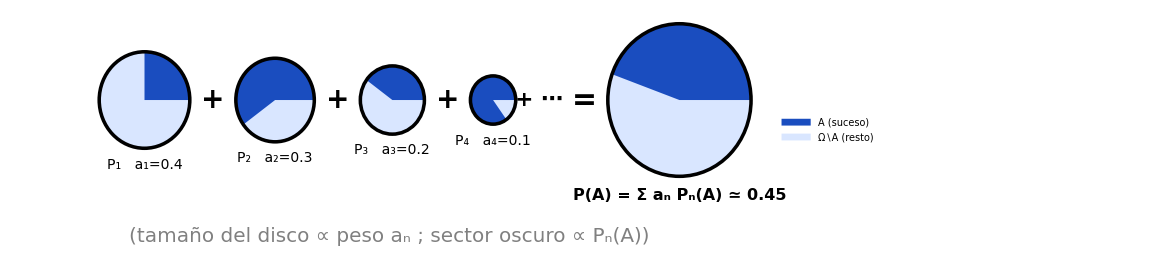

```mathematica
(*Ejemplo ilustrativo truncado a 4 términos (en el enunciado la suma es infinita)*)an={0.4,0.3,0.2,0.1};    (*pesos a_n,deben sumar 1*)
pn={0.25,0.6,0.4,0.85};  (*valores P_n(A) para el mismo suceso A*)
nTerm=Length[an];

escala=1.4; (*tamaño global de los discos*)
radios=escala Sqrt[an];           (*radio proporcional a sqrt(a_n):area~a_n*)
radioFinal=escala Sqrt[Total[an]];

colorFondo=RGBColor[0.85,0.9,1];  (*Omega\ A*)
colorA=RGBColor[0.1,0.3,0.75];    (*A*)

PA=Total[an pn]; (*P(A)=suma a_n P_n(A),calculado automáticamente*)

subDigit[d_Integer]:=FromCharacterCode[8320+d];
subInd[k_Integer]:=StringJoin[subDigit/@IntegerDigits[k]];

discoMedida[centro_,r_,p_]:={colorFondo,Disk[centro,r],colorA,Disk[centro,r,{0,2 Pi p}],Black,Thickness[0.003],Circle[centro,r]};

(*Posiciones de los discos,uno tras otro,dejando hueco para los signos "+"*)
gap=0.9;
centrosX=Table[0,{nTerm}];
centrosX[[1]]=radios[[1]];
Do[centrosX[[i]]=centrosX[[i-1]]+radios[[i-1]]+gap+radios[[i]],{i,2,nTerm}];

discos=Table[discoMedida[{centrosX[[k]],0},radios[[k]],pn[[k]]],{k,nTerm}];

signosMas=Table[Text[Style["+",28,Bold],{(centrosX[[k]]+radios[[k]]+centrosX[[k+1]]-radios[[k+1]])/2,0}],{k,1,nTerm-1}];

etiquetasDiscos=Table[Text[Style["P"<>subInd[k]<>"   a"<>subInd[k]<>"="<>ToString[an[[k]]],14],{centrosX[[k]],-radios[[k]]-0.3}],{k,nTerm}];

xElipsis=centrosX[[nTerm]]+radios[[nTerm]]+gap/2;
elipsis=Text[Style["+ ⋯",22,Bold],{xElipsis,0}];

xIgual=xElipsis+gap;
igual=Text[Style["=",30,Bold],{xIgual,0}];

xFinal=xIgual+gap/2+radioFinal;
discoFinal=discoMedida[{xFinal,0},radioFinal,PA];
etiquetaFinal=Text[Style["P(A) = Σ aₙ Pₙ(A) ≃ "<>ToString[NumberForm[PA,{3,2}]],16,Bold],{xFinal,-radioFinal-0.35}];

notaTamano=Text[Style["(tamaño del disco ∝ peso aₙ ; sector oscuro ∝ Pₙ(A))",20,Italic,Gray],{xFinal/2,-escala-1.1}];

grafico=Graphics[{discos,signosMas,etiquetasDiscos,elipsis,igual,discoFinal,etiquetaFinal,notaTamano},PlotRange->All,PlotRangePadding->{{0.3,0.3},{0.3,0.6}},ImageSize->850];

imagenFinal=Legended[grafico,SwatchLegend[{colorA,colorFondo},{"A (suceso)","Ω∖A (resto)"},LabelStyle->Directive[FontSize->16],LegendMarkerSize->20]];

imagenFinal
```

```mathematica
Export["prob_quesada_2_1_a.png",imagenFinal,Background->None,ImageResolution->1200];
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["prob_quesada_2_1_a.png"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["prob_quesada_2_1_a.png"]]]
```